Boolean Algebra

## Introduction

In this chapter, we will use Mathematica to model Boolean algebra. In Section 1, we demonstrate the basic functions that will be used in this chapter. In Section 2, we will focus on the disjunctive normal form of a logical expression. We will see how to use Wolfram Language functions for finding a disjunctive normal form expression for a Boolean function and for finding a representation for a function defined by a table of values. In Section 3, we will see how logical circuits can be modeled in the Wolfram Language, including how to go about transforming a circuit diagram into an expression. We also provide a function that will transform a logical expression into a model of a circuit. In the final section of the chapter, we consider simplification of logical expressions, and we develop an implementation of the Quine–McCluskey method.

## 12.1 Boolean Functions

In this section, we will see how to work with Boolean expressions and how to create Boolean functions. We will also use Mathematica to verify identities in Boolean algebra and to compute the dual of an expression.

### Preliminaries

In Chapter 1 of this manual, we discussed logical expressions in the Wolfram Language. The Boolean values true and false are represented by the symbols True and False. In the Wolfram Language, these are constant values, like the numbers 2 or Pi.

We also saw the logical operators And (&&), Or (||), and Not (!) in Chapter 1. These can be used in functional form or as operators. The following two expressions both compute T∧¬(T∨F).

```mathematica
True&&!(True||False)
```

False

```mathematica
And[True,Not[Or[True,False]]]
```

False

Note that the Wolfram Language respects the usual order of precedence for logical operators, namely negation followed by conjunction, then disjunction, and finally implication.

Other logical operators supported by the Wolfram Language include: the exclusive or, Xor, implication, Implies, and the biconditional, Equivalent. Each logical connective can be entered as a mathematical symbol by using an escape sequence, as shown in the table below.

And | EscandEsc | ∧
Or | EscorEsc | ∨
Not | EscnotEsc | ¬
Xor | EscxorEsc | ⊻
Implies | Esc=>Esc | ⇒
Equivalent | EscequivEsc | ⧦

In this manual, except for And (&&), Or (||), and Not (!) whose infix forms are simple keyboard characters, we will typically enter operators in functional form, rather than using the escape sequences.

For Boolean algebra, the textbook uses the objects 0 and 1 with operators +, ·, and OverBar[] instead of their logical counterparts. It is tempting to use the Wolfram Language’s bit functions, BitAnd, BitOr, and BitNot, in order to replicate the 0-1 form of Boolean expressions. However, the bit functions behave differently than the corresponding Boolean operators would—in particular BitNot does not switch between 0 and 1.

```mathematica
BitNot[0]
```

-1

```mathematica
BitNot[1]
```

-2

In the remainder of this manual, we will stick to the logical forms of Boolean expressions. However, some readers may be interested to know that it is possible to create operators to mirror the kinds of Boolean algebra expressions used in the text. To do so, we use symbols that the Wolfram Language will interpret as operators but which have no built-in definition. For example, we could use circle times (⊗, entered Escc*Esc) and circle plus (⊕, entered Escc+Esc) for the and and or operators, and the overbar (OverBar[□], entered by highlighting the expression to be negated and typing Ctrl +& followed by the underscore,  _) for negation. Then, the expression 1·0+OverBar[(0+1)] would be entered as shown below.

```mathematica
1⊗0⊕OverBar[0⊕1]
```

1⊗0⊕OverBar[0⊕1]

```mathematica
FullForm[%]
```

CirclePlus[CircleTimes[1,0],OverBar[CirclePlus[0,1]]]

To get Mathematica to evaluate such expressions properly, you just need to make definitions to the symbols. By setting the Flat and Listable attributes first, the operator will be associative. For example, ⊗ can be defined by setting values for CircleTimes.

```mathematica
SetAttributes[CircleTimes,{Flat,Listable}];
CircleTimes[1,1]=1;
CircleTimes[1,0]=0;
CircleTimes[0,1]=0;
CircleTimes[0,0]=0;
```

Mathematica will now automatically simplify ⊗, so if we enter the previous expression again:

```mathematica
1⊗0⊕OverBar[0⊕1]
```

0⊕OverBar[0⊕1]

Definitions of the other operations are left to the interested reader. In this manual, we will not use this approach, since the logical form of Boolean expressions is more naturally supported by the Wolfram Language.

### Boolean Expressions and Boolean Functions

Consider Example 1 from the textbook, which asks that we compute the value of 1·0+OverBar[(0+1)]. To perform this computation in Mathematica, we first translate it into a logical statement. We do this by changing 1 into True, 0 into False, the multiplication into And (&&), the addition into Or (||), and the bar into Not (!).

```mathematica
True&&False||!(False||True)
```

False

Of course, you can enter Boolean expressions involving variables, assuming the symbols have not previously been assigned values.

```mathematica
Implies[p&&q,r]
```

p&&q⇒r

Moreover, just as with arithmetic expressions, you can evaluate these expressions for specific values by applying the ReplaceAll (/.) operator.

```mathematica
Implies[p&&q,r]/.{p->True,q->True,r->False}
```

False

#### Representing Boolean Functions

You define a Boolean function in the Wolfram Language in the same way as any other function.

Consider, for example, the Boolean function f(x,y,z)=x y+y z+z x (written in the 0-1 notation).

This can be modeled in the Wolfram Language by the function defined below.

```mathematica
f[x_,y_,z_]:=Or[And[x,y],And[y,z],And[z,x]]
```

You can work with f in the usual way. The following applies f to p, q, and r.

```mathematica
f[p,q,r]
```

(p&&q)||(q&&r)||(r&&p)

When f is applied to truth values, it is evaluated.

```mathematica
f[True,False,True]
```

True

You can also mix truth values and symbols. In this case, Mathematica will simplify the expression, given the partial information.

```mathematica
f[True,q,r]
```

q||(q&&r)||r

You may notice that this expression is logically equivalent to q∨r. Applying the Simplify function will cause Mathematica to more fully simplify the output.

```mathematica
f[True,q,r]//Simplify
```

q||r

#### Values of Boolean Functions

Examples 4 and 5 of Section 12.1 illustrate how the values of a Boolean function, in the 0-1 format, can be displayed in a table. In the logical form, this is equivalent to a truth table for the Boolean function. In Chapter 1, we illustrated the use of the BooleanTable function for creating truth tables.

Recall that BooleanTable accepts two arguments: a Boolean expression and a list of the variables. The output is a list of the truth values for the expression obtained by substituting every possible combination of truth values into the variables.

For example, we will display the table of values for the Boolean function f defined above. The first argument to BooleanTable will be a list containing the three variables and the function applied to them. Giving the first argument as this list means that the output will indicate the values of the individual variables, and not just the result. The second argument will be the list of variables.

```mathematica
BooleanTable[{p,q,r,f[p,q,r]},{p,q,r}]//TableForm
```

True | True | True | True
True | True | False | True
True | False | True | True
True | False | False | False
False | True | True | True
False | True | False | False
False | False | True | False
False | False | False | False

If you wish, you can use this function to produce output in the 0-1 form by applying the Boole function. Boole is a built-in function that transforms the truth values True and False into the values 1 and 0. Since it threads over lists, it can be applied to the output from BooleanTable.

```mathematica
Boole[BooleanTable[{p,q,r,f[p,q,r]},{p,q,r}]]//TableForm
```

1 | 1 | 1 | 1
1 | 1 | 0 | 1
1 | 0 | 1 | 1
1 | 0 | 0 | 0
0 | 1 | 1 | 1
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0

We can further refine the output by using the TableHeadings option for TableForm. TableHeadings is assigned to a pair representing the row and column headings, with None used when a group of headings is not wanted.

```mathematica
TableForm[Boole[BooleanTable[{p,q,r,f[p,q,r]},{p,q,r}]],TableHeadings->{None,{"p","q","r","f(p,q,r)"}}]
```

p | q | r | f(p,q,r)
1 | 1 | 1 | 1
1 | 1 | 0 | 1
1 | 0 | 1 | 1
1 | 0 | 0 | 0
0 | 1 | 1 | 1
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0

#### Operations on Boolean Functions

As with functions on real numbers, Boolean functions can be combined using basic operations. The complement of a Boolean function and the Boolean sum and product of functions are defined in the text.

To compute complements, sums, and products of Boolean functions, you must define a new function in terms of the original. For example, consider the function G(x,y)=x·y. In logical notation, this is G(x,y)=x∧y.

```mathematica
G[x_,y_]:=x&&y
```

The complement of G, which we name notG, is created as follows. The arguments of notG are the same as G. The formula that defines notG is !G[x,y].

```mathematica
notG[x_,y_]:=!G[x,y]
```

Observe that if we evaluate notG at a pair of variables, Mathematica returns the expected result.

```mathematica
notG[x,y]
```

!(x&&y)

Let us define another function, H(x,y)=x·ȳ.

```mathematica
H[x_,y_]:=x&&!y
```

To compute the Boolean sum G+H, we combine the functions with the Or (||) operator. More precisely, we define a function GpH with the formula G[x,y]||H[x,y].

```mathematica
GpH[x_,y_]:=G[x,y]||H[x,y]
```

Applying this to a pair of variables and simplifying, we obtain the following formula for G+H.

```mathematica
GpH[x,y]//Simplify
```

x

This result indicates that x·y+x·ȳ=x. This can also be verified using the identities in Table 5 of Section 12.1.

### Identities of Boolean Algebra

We can check identities, equivalence of Boolean expressions, and equality of Boolean functions using the Equivalent and TautologyQ functions.

We will use the distributive law, x(y+z)=x·y+x·z, as an example. First, we must translate the statement into a logical equivalence: x∧(y∨z)≡(x∧y)∨(x∧z).

Now, we will assign the expressions on either side of the equivalence to symbols. This is not necessary, but it will make later expressions easier to read.

```mathematica
distributiveL=x&&(y||z);
distributiveR=(x&&y)||(x&&z);
```

To confirm the equivalence of the two Boolean expressions, we combine them into a biconditional using the Equivalent function. We then apply the TautologyQ function to the biconditional and a list of the Boolean variables appearing in the expression.

```mathematica
TautologyQ[Equivalent[distributiveL,distributiveR],{x,y,z}]
```

True

This verifies the given distributive law.

In the case that the two expressions are not equivalent, you can use the SatisfiabilityInstances function to find a list of assignments of truth values to the variables in the expression that demonstrates that the expressions are not equivalent.

Consider the nonequivalence x+x·y≠y. In logical form, this is x∨(x∧y)≢y. First, observe that TautologyQ returns false.

```mathematica
TautologyQ[Equivalent[x||(x&&y),y],{x,y}]
```

False

Now, apply SatisfiabilityInstances to the negation of the equivalence.

```mathematica
SatisfiabilityInstances[!Equivalent[x||(x&&y),y],{x,y}]
```

{{True,False}}

This output means that setting x equal to true and y equal to false provides a demonstration, by counterexample, that x∨(x∧y)≢y. Indeed, substituting x=true and y=false on the left-hand side produces true∨(true∧false)≡true∨false≡true. That is not the same as the right-hand side, y, which is assigned false.

Note that the output from SatisfiabilityInstances is a list of assignments. Ordinarily, only one truth value assignment will be returned. However, if you provide a positive integer as an optional third argument, Mathematica will attempt to find that number of different assignments. Below, we ask for three assignments, but only two exist and so two are returned.

```mathematica
SatisfiabilityInstances[!Equivalent[x||(x&&y),y],{x,y},3]
```

{{True,False},{False,True}}

Equality of Boolean functions can also be checked with the Equivalent and TautologyQ functions.

Consider the following Boolean functions.

f_1(x,y)=OverBar[(x·y)]

f_2(x,y)=x̄+ȳ

Define the corresponding functions:

```mathematica
f1[x_,y_]:=!(x&&y);
f2[x_,y_]:=!x||!y;
```

We can test the assertion that f_1(x,y)=f_2(x,y) by applying the Equivalent and TautologyQ functions as shown below.

```mathematica
TautologyQ[Equivalent[f1[x,y],f2[x,y]],{x,y}]
```

True

### Duality

We conclude this section by showing how Mathematica can be used to compute the dual of an expression. We will define a function, dual, to achieve this.

Recall that the dual of a Boolean expression is the expression obtained by interchanging conjunctions and disjunctions and interchanging true and false. We can achieve this by applying ReplaceAll (/.) with a list of rules effecting the interchanges.

```mathematica
dual[expr_]:=expr/.{And->Or,Or->And,False->True,True->False}
```

Note that this will not produce an infinite loop, since ReplaceAll (/.) operates by looking at each part of the expression only once and applies the first rule in the list that is valid.

For example, consider the expression x·ȳ+y·z̄+x̄·z. As a logical expression, this can be written as (x∧¬y)∨(y∧¬z)∨(¬x∧z). We calculate the dual by applying the dual function.

```mathematica
dual1=dual[(x&&!y)||(y&&!z)||(!x&&z)]
```

(x||!y)&&(y||!z)&&(!x||z)

Similarly, the dual of x̄·y+ȳ·z+x·z̄ can be computed by

```mathematica
dual2=dual[(!x&&y)||(!y&&z)||(x&&!z)]
```

(!x||y)&&(!y||z)&&(x||!z)

Exercise 13 of Section 12.1 asks you to prove that the expressions x·ȳ+y·z̄+x̄·z and x̄·y+ȳ·z+x·z̄ are equivalent. The duality principle implies that the duals calculated above are also equivalent. This can be verified by the Equivalent and TautologyQ functions.

```mathematica
TautologyQ[Equivalent[dual1,dual2],{x,y,z}]
```

True

## 12.2 Representing Boolean Functions

In this section, we will see how to express Boolean functions in the disjunctive normal form (also called sum-of-products expansion). We will first look at the Wolfram Language function for turning an expression in Boolean algebra into the disjunctive normal form. Then, we will see the function for finding an expression based on a table of values.

### Disjunctive Normal Form from an Expression

Given an expression written using the logical connectives, the BooleanConvert function can be used to transform the expression into disjunctive normal form.

Consider Example 3 from Section 12.2 of the main text: (x+y)z̄. In logical form, this is (x∨y)∧¬z. We assign this logical expression to a symbol.

```mathematica
example3=(x||y)&&!z
```

(x||y)&&!z

The most common way to apply the BooleanConvert function involves two arguments: the expression to be converted and a string representing the desired form of the output. There are several possible forms, as detailed by the help page, but the two we will be using are "DNF" for disjunctive normal form (or equivalently "SOP" meaning sum of products) and "CNF" for conjunctive normal form (or equivalently "POS" meaning product of sums). Be sure to include the quotation marks.

Below, we convert example3 to disjunctive normal form using "DNF" in the second argument.

```mathematica
BooleanConvert[example3,"DNF"]
```

(x&&!z)||(y&&!z)

Note that this expression is different from the solution to Example 3 in the text. Mathematica produces a reduced disjunctive normal form in which terms are not required to contain every variable.

BooleanConvert can also be applied with a single argument, in which case it defaults to disjunctive normal form.

```mathematica
BooleanConvert[example3]
```

(x&&!z)||(y&&!z)

To produce conjunctive normal form, "CNF" (or "POS") is required as the second argument.

```mathematica
BooleanConvert[example3,"CNF"]
```

(x||y)&&!z

### Disjunctive Normal Form from a Table

Example 1 of Section 12.2 describes how to find an expression for a Boolean function represented by a table of values. We will illustrate the built-in Wolfram Language functions that accomplish this task.

To define a Boolean function using truth values, we use BooleanFunction. This function has a variety of uses, including the ability to specify a Boolean function in terms of the number variables and an index into the list of all Boolean functions on that number of variables, and the ability to specify a Boolean function in terms of truth value assignments. We will focus on the latter.

For example, consider the function defined by the following table.

x | y | z | F(x,y,z)
1 | 1 | 1 | 0
1 | 1 | 0 | 1
1 | 0 | 1 | 0
1 | 0 | 0 | 1
0 | 1 | 1 | 0
0 | 1 | 0 | 1
0 | 0 | 1 | 1
0 | 0 | 0 | 0

There are two ways we can represent this function in the Wolfram Language that will be usable as input to BooleanFunction. The first is as rules that assign the truth value assignments to the value of the function. For example, the third row in the table would correspond to the rule {1,0,1}→0. Note that BooleanFunction allows for the use of 0-1 notation for true and false. It will also accept the symbols True and False, as in {True,False,True}→False. We will use the 0-1 notation as it makes for shorter input sequences.

Given a list of such rules, the BooleanFunction will output a Mathematica function object.

```mathematica
BFexample=BooleanFunction[{{1,1,1}->0,{1,1,0}->1,{1,0,1}->0,{1,0,0}->1,{0,1,1}->0,{0,1,0}->1,{0,0,1}->1,{0,0,0}->0}]
```

BooleanFunction[…]

Applying the function to truth values yields the appropriate result.

```mathematica
BFexample[True,False,True]
```

False

With a list of variable names as a second argument, BooleanFunction will output an expression for the Boolean function instead of a BooleanFunction object.

```mathematica
BooleanFunction[{{1,1,1}->0,{1,1,0}->1,{1,0,1}->0,{1,0,0}->1,{0,1,1}->0,{0,1,0}->1,{0,0,1}->1,{0,0,0}->0},{x,y,z}]
```

(x&&!z)||(!x&&!y&&z)||(y&&!z)

A third argument can be used to specify the form, for example, “DNF” or “CNF”, for the output.

```mathematica
BooleanFunction[{{1,1,1}->0,{1,1,0}->1,{1,0,1}->0,{1,0,0}->1,{0,1,1}->0,{0,1,0}->1,{0,0,1}->1,{0,0,0}->0},{x,y,z},"CNF"]
```

(!x||!z)&&(x||y||z)&&(!y||!z)

You can simplify the input to BooleanFunction slightly by entering only those rules corresponding to one of the possible function values, say true, and then use a BlankSequence (__) to assert that all others have the other value. This is illustrated below for the same function,

```mathematica
BooleanFunction[{{1,1,0}->1,{1,0,0}->1,{0,1,0}->1,{0,0,1}->1,{__}->0},{x,y,z},"CNF"]
```

(!x||!z)&&(x||y||z)&&(!y||!z)

Observe that this is identical to the output above.

You can simplify the input even further by entering only the output values of the function, provided you enter them in standard order. The order the values must be entered in is the same as displayed in the table above.

```mathematica
BooleanFunction[{0,1,0,1,0,1,1,0},{x,y,z}]
```

(x&&!z)||(!x&&!y&&z)||(y&&!z)

If you are in doubt of the order in which to enter the function’s values, it is identical to the order used by BooleanTable, the function used to display truth tables. Below, we use BooleanTable to display the canonical ordering of truth value assignments for two variables.

```mathematica
BooleanTable[{x,y},{x,y}]//TableForm
```

True | True
True | False
False | True
False | False

## 12.3 Logic Gates

In this section, we will use Mathematica to work with logic gates, particularly circuit diagrams. First, we will see how to translate a circuit diagram into a Boolean expression. Then, we will do the reverse and see how to transform a logical expression into a circuit diagram (modeled as a tree diagram).

### Circuit Diagram to Logical Expression

Consider the circuit diagram shown below.

-Graphics-

Our goal in this section is to produce a logical expression for the output of this diagram.

To do this, we use the fact that the Wolfram Language has functional forms for each of the logical expressions. That is, Not, And, and Or can all be used as functions applied to expressions. For example, the following forms the disjunction of x, y, and z.

```mathematica
Or[x,y,z]
```

x||y||z

We give each gate in the diagram a label. The specific names are not important. We chose to label the gates using the capital letter G with subscripts numbered from the right to the left.

-Graphics-

Interpret the labels as names for both the gates themselves and for their outputs. Note that G_1 is the name for both the output of the final gate and also names the output of the circuit. The input of G_1 is the outputs from gates G_2 and G_3. That is to say, G_1=G_2 OR G_3.We can write that in the Wolfram Language as shown below.

```mathematica
G1=Or[G2,G3]
```

G2||G3

For each gate, do the same. Note that the order in which the gates are specified is irrelevant. The gate G_2 is a AND b.

```mathematica
G2=And[a,b]
```

a&&b

The output of G_3 is the conjunction of G_4, b, and G_5.

```mathematica
G3=And[G4,b,G5]
```

G4&&b&&G5

Gates G_4 and G_5 are inversions on a and c, respectively.

```mathematica
G4=Not[a]
```

!a

```mathematica
G5=Not[c]
```

!c

Once all of the gates have been specified, inspect the value for the final gate, G_1.

```mathematica
G1
```

(a&&b)||(!a&&b&&!c)

This tells us that the circuit’s result is (a∧b)∨(¬a∧b∧¬c). In 0-1 form, this is ab+ā b c̄.

The reason this works is that when we define the output of a gate in terms of unassigned names, such as G_2, Mathematica accepts the definition. When G_2 is later assigned its own value and then the expression for G_1 is evaluated, Mathematica resolves all assigned names into their definitions so that the expression for G_1 is in terms of unassigned names (a, b, and c) only.

### Logical Expression to Circuit Diagram

We have just seen how to use Mathematica to transform a circuit diagram into a logical expression for the result of the circuit. Now, we consider the reverse. Given a logical expression, such as that for G_1, we will transform the expression into a circuit diagram.

We will model a circuit diagram as an ordered rooted tree. While circuit diagrams are not necessarily ordered, making the tree ordered will allow for the possibility of including Boolean functions as subcircuits.

Vertices in the tree will correspond to gates in the circuit. One of the vertices is distinguished as the root, which will correspond to the final gate, whose output is the output of the circuit. Each vertex has a number of children vertices. The edge between a vertex and its child corresponds to the input to the gate. Each vertex other than the root has a parent, and the edge from the vertex to the parent corresponds to the output from the gate.

The assumption that a circuit can be modeled as a tree requires that the circuit satisfy the following properties. First, the circuit has only one output. Second, each gate has only one output. Third, there are no branches (e.g., an input cannot be used as input to more than one gate). Given that our goal is to begin with a logical expression and create a corresponding abstract circuit, these restrictions are of little importance. If we were actually building physical circuits, there would be efficiency concerns.

Recall that in Chapter 11, we wrote the function expressionTree for converting an algebraic expression in terms of the arithmetic operators into a tree representation. We will make use of the functions from Chapter 11 here, and have included them in the package for this chapter. If you place the file Chapter12.wl from the website in the same directory as this notebook is stored, then executing the following expression will load the needed functions from Chapter 11, as well as those defined in this chapter..

```mathematica
<<(NotebookDirectory[]<>"Chapter12.wl")
```

Apply the expressionTree function from Chapter 11 to the logical expression we obtained from the circuit diagram above.

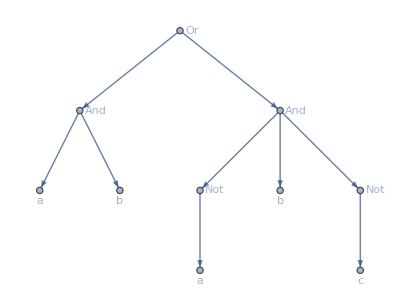

```mathematica
expressionTree[G1]
```

Observe that the original circuit diagram and the tree have the same structure. After reversing the arrows, rotating by 90°, and exchanging the symbols with the functions labeling the internal nodes, the two are identical.

## 12.4 Minimization of Circuits

In this section, we will discuss the use of the Wolfram Language BooleanMinimize function for minimizing circuits, and we will provide an implementation of the Quine–McCluskey method.

### The BooleanMinimize Function

The BooleanMinimize function, applied to a Boolean expression, finds a minimal representation of the expression in disjunctive normal form.

For example, we apply BooleanMinimize to the expression we obtained for the output of the circuit diagram at the beginning of Section 12.3 of this manual.

```mathematica
BooleanMinimize[(a&&b)||(!a&&b&&!c)]
```

(a&&b)||(b&&!c)

The result indicates that ¬a can be removed as an input to the second AND gate.

The result of BooleanMinimize is guaranteed to be of minimal length among all possible disjunctive normal form representations of the input, however, such a minimal expression is not unique. Note that if you do not care that the expression be in disjunctive normal form, the Simplify function will produce a shorter expression.

```mathematica
Simplify[(a&&b)||(!a&&b&&!c)]
```

(a||!c)&&b

The BooleanMinimize function can also accept, as a second argument, all the same forms as BooleanConvert in order to produce minimal expressions of different forms. For example, to find a minimal conjunctive normal form expression, you enter the following:

```mathematica
BooleanMinimize[(a&&b)||(!a&&b&&!c),"CNF"]
```

(a||!c)&&b

### Don’t Care conditions

Informally, a set of don’t care conditions for a Boolean function F is a set of points in the domain of F whose images do not concern us.

If F is a function on n variables, then its domain is {true,false}^n. Let A be the subset of {true,false}^n for which the value of F is specified. If we think of F as fully defined on this subset A, then we are interested in the family of all extensions of F to all of {true,false}^n. In other words, the set of all G defined on {true,false}^n that agree with F on A. The goal is to choose the simplest such G. That is, the G that has the smallest sum of products expansion.

We should pause to consider the size of this problem. If there are d don’t care points, then there are 2^d possible extensions G. Considering every possible extension can become rather time consuming.

Consider the Boolean function F defined by the following table of values, in which “d” in the final column indicates a don’t care condition.

x | y | z | F(x,y,z)
true | true | true | true
true | true | false | false
true | false | true | false
true | false | false | true
false | true | true | d
false | true | false | d
false | false | true | false
false | false | false | true

The points that must evaluate to true are: {(false,false,false),(true,false,false),(true,true,true)} and the don’t care conditions are {(false,true,false),(false,true,true)}.

In Section 12.2, we showed how to use BooleanFunction to define a Boolean function in terms of a table. We also saw above that you can specify a default output by using a BlankSequence (__). For example, the following returns the Boolean expression that is true on (true,false,true,false) and false otherwise.

```mathematica
BooleanFunction[{{True,False,True,False}->True,{__}->False},{x,y,z,w}]
```

!w&&x&&!y&&z

We can specify a don’t care condition within a call to BooleanFunction by identifying a don’t care condition, for example, (false,true,false), with a Blank (_) as the result.

Therefore, we can determine a Boolean function defined by the table above as follows.

```mathematica
BooleanFunction[{{True,True,True}->True,
{True,True,False}->False,
{True,False,True}->False,
{True,False,False}->True,
{False,True,True}->_,
{False,True,False}->_,
{False,False,True}->False,
{False,False,False}->True},
{x,y,z}]
```

(x&&y&&z)||(!x&&!z)||(!y&&!z)

### Quine–McCluskey

We conclude with an implementation of the Quine–McCluskey method. This method is fairly involved and it will take considerable effort to implement it correctly, but understanding this algorithm is worthwhile.

It will be helpful to have an example that we can use to illustrate the method as we build the function. The expression we use for the example is

w x ȳ z̄+w x̄ y z+w x̄ y z̄+w x̄ ȳ z̄+w̄ x y z+w̄ x ȳ z+w̄ x ȳ z̄+w̄ x̄ y z+w̄ x̄ ȳ z+w̄ x̄ ȳ z̄

We assign this to the symbol F.

```mathematica
F=(w&&x&&!y&&!z)||(w&&!x&&y&&z)||(w&&!x&&y&&!z)||(w&&!x&&!y&&!z)||(!w&&x&&y&&z)||(!w&&x&&!y&&z)||(!w&&x&&!y&&!z)||(!w&&!x&&y&&z)||(!w&&!x&&!y&&z)||(!w&&!x&&!y&&!z);
```

Let us begin by (very) briefly outlining the approach. More details will be given as we proceed.

Transform the minterms into bit strings.

Group the bit strings by the number of 1s.

Combine bit strings that differ in exactly one location.

Repeat steps 2 and 3 until no additional combinations are possible.

Identify the prime implicants (those bit strings not used in a simplification) and form the coverage table.

Identify the essential prime implicants and update the table.

Process the remaining prime implicants using a heuristic approach in order to achieve complete coverage.

Implementing this will require several different functions that will come together to achieve the goal of minimizing the expression for F.

#### Modifying Arguments

Before we begin implementing the method, we take a moment to explain the HoldRest attribute. Earlier in this manual, we have seen how to use a held argument to allow modification of an argument to a function. We will need to do this again here in order to avoid the need to copy data structures that must be modified by a function.

Holding parameters to a function means that, when you call the function on a symbol, instead of applying the function to the object stored in that symbol, the function is given the name of the symbol itself. This allows the symbol name to be reassigned and otherwise modified within the function.

The HoldRest attribute causes all but the first argument to a function to be held. For example, the following function updates the symbol given as the second argument to be the sum of what it previously stored and the first argument, and appends the result to the list associated to the symbol given as the third argument.

```mathematica
exampleHold1=5;
exampleHold2=12;
exampleHold3={1,2,3};
SetAttributes[exampleHoldFunction,{HoldRest}];
exampleHoldFunction[a_,b_,c_]:=Module[{},
b=a+b;
AppendTo[c,b]
]
```

```mathematica
exampleHoldFunction[exampleHold1,exampleHold2,exampleHold3]
```

{1,2,3,17}

Observe that the values stored in the last two arguments have changed. Without the HoldRest attribute, both expressions in the body of the Module would have produced errors.

```mathematica
exampleHold2
```

17

```mathematica
exampleHold3
```

{1,2,3,17}

Other attributes that can be used to hold arguments are HoldFirst and HoldAll.

#### Transforming Minterms Into Bit Strings

The first task is to process the input. That is, F must be transformed into a list of bit strings. This is not strictly necessary, but it makes working with the minterms more convenient. We represent bit strings as lists of 0s and 1s.

We begin by creating a function to transform a single minterm into a bit string. We assume that the input to this function will be a properly formed minterm, that is, a conjunction of variables and negations of variables. We require that a list of variables be provided to the function, so that the bit string can be formed in the proper order.

Consider the following minterm, which is the fourth minterm in our example F.

```mathematica
minterm=w&&!x&&y&&!z
```

w&&!x&&y&&!z

Fortunately, Mathematica automatically interprets a series of conjunctions into a single application of the And (&&) function with multiple arguments. Applying FullForm illustrates.

```mathematica
FullForm[minterm]
```

And[w,Not[x],y,Not[z]]

MemberQ’s first argument can have any head, not just a List. So, we can determine that w is part of the conjunction but that x is not by applying MemberQ to minterm and the variables.

```mathematica
MemberQ[minterm,w]
```

True

```mathematica
MemberQ[minterm,x]
```

False

But of course, the negation of x is part of minterm.

```mathematica
MemberQ[minterm,Not[x]]
```

True

To transform the minterm into a bit string, we only need to check, for each variable, whether the variable or its negation is in the list. Recall that we will insist that the function be given the list of variables as an argument to maintain the proper order of the variables.

We first assign the list of variables to a symbol.

```mathematica
variableList={w,x,y,z}
```

{w,x,y,z}

Now, create a list, initialized to the proper length, for the bit string.

```mathematica
bitstring=ConstantArray[Null,4]
```

{Null,Null,Null,Null}

Finally, we use a For loop to check, for each variable in the variable list, whether the variable is in the minterm. If the variable is a member of minterm, then we change the bit to 1. If the negation is in minterm, we set the value in the bit string to 0. Otherwise, we place the character “-” in the list, to indicate the absence of the variable in the string.

```mathematica
For[i=1,i≤Length[variableList],i++,
Which[MemberQ[minterm,variableList[[i]]],bitstring[[i]]=1,
MemberQ[minterm,Not[variableList[[i]]]],bitstring[[i]]=0,
True,bitstring[[i]]="-"]
]
```

This has created the bit string associated to minterm.

```mathematica
bitstring
```

{1,0,1,0}

We condense this process into a single function. Note the use of Which. Recall that the result of Which is the argument in an even position following the first odd-positioned argument that evaluates to true.

```mathematica
mtToBitstring[minterm_,variableList_]:=Module[{i,bitstring},
bitstring=ConstantArray[Null,Length[variableList]];
For[i=1,i≤Length[variableList],i++,
Which[MemberQ[minterm,variableList[[i]]],
bitstring[[i]]=1,
MemberQ[minterm,Not[variableList[[i]]]],
bitstring[[i]]=0,
True,
bitstring[[i]]="-"
]
];
bitstring
]
```

```mathematica
mtToBitstring[minterm,{w,x,y,z}]
```

{1,0,1,0}

#### Transforming the Original Expression Into Bit Strings

Now that we have the means for transforming a single minterm into a bit string, we are ready to transform an expression in disjunctive normal form into a list of bit strings.

Observe that an expression in disjunctive normal form is the Or (||) function applied to minterms. Again, FullForm reveals this convenient structure.

```mathematica
FullForm[F]
```

Or[And[w,x,Not[y],Not[z]],And[w,Not[x],y,z],And[w,Not[x],y,Not[z]],And[w,Not[x],Not[y],Not[z]],And[Not[w],x,y,z],And[Not[w],x,Not[y],z],And[Not[w],x,Not[y],Not[z]],And[Not[w],Not[x],y,z],And[Not[w],Not[x],Not[y],z],And[Not[w],Not[x],Not[y],Not[z]]]

Our goal is to produce a list of the bit strings obtained from the minterms. We can transform the disjunction into a list by using the Apply (@@) function to replace the Or (||) head with a List head.

```mathematica
List@@F
```

{w&&x&&!y&&!z,w&&!x&&y&&z,w&&!x&&y&&!z,w&&!x&&!y&&!z,!w&&x&&y&&z,!w&&x&&!y&&z,!w&&x&&!y&&!z,!w&&!x&&y&&z,!w&&!x&&!y&&z,!w&&!x&&!y&&!z}

Then, we just need to apply the mtToBitstring function to each member of the list. We can do this by using the Map (/@) function, which applies a function (given as the first argument) to a list (given as the second argument) and returns the list obtained by applying the function to each element of the list. Since the mtToBitstring requires two arguments, not just one, the first argument to Map (/@) will be a pure Function (&) obtained by calling mtToBitstring on a Slot (#) and the list of variables.

```mathematica
Map[mtToBitstring[#,{w,x,y,z}]&,List@@F]
```

{{1,1,0,0},{1,0,1,1},{1,0,1,0},{1,0,0,0},{0,1,1,1},{0,1,0,1},{0,1,0,0},{0,0,1,1},{0,0,0,1},{0,0,0,0}}

We define a function based on this model. Note that the above presumed that there was more than one minterm. We define the function with different signatures to ensure that it will correctly handle a single minterm.

```mathematica
dnfToBitList[dnfExpr_Or,variableList_]:=Map[mtToBitstring[#,variableList]&,List@@dnfExpr];
dnfToBitList[dnfExpr_And,variableList_]:={mtToBitstring[dnfExpr,variableList]}
```

We now apply this function to the example expression and store the result as the symbol Fbits.

```mathematica
Fbits=dnfToBitList[F,{w,x,y,z}]
```

{{1,1,0,0},{1,0,1,1},{1,0,1,0},{1,0,0,0},{0,1,1,1},{0,1,0,1},{0,1,0,0},{0,0,1,1},{0,0,0,1},{0,0,0,0}}

#### Transforming Bit Strings Into Minterms

At the conclusion of the Quine–McCluskey process, we will want to display the result in disjunctive normal form. This will require that we turn bit strings back into minterms.

Note that since this function will be applied at the end of the process, it may be that some of the variables have been removed. We will be using the string “-” in a bit string to indicate the elimination of a variable.

This function will require the bit string and a list of variable names as its input. It operates in two stages. First, it processes the variable list based on the content of the bit string. It initializes an empty list and, for each variable, appends the variable or its negation or does nothing, depending on the content of the bit string.

```mathematica
bitstr={0,1,"-",0}
```

{0,1,-,0}

```mathematica
outList={}
```

{}

```mathematica
For[i=1,i≤Length[variableList],i++,
Switch[bitstr[[i]],
1,AppendTo[outList,variableList[[i]]],
0,AppendTo[outList,Not[variableList[[i]]]],
"-",Null]
]
```

```mathematica
outList
```

{!w,x,!z}

Note the use of the Switch function. Recall that Switch evaluates its first argument, and then compares that result to the arguments with even index, executing the argument following the first of the even-indexed arguments that matches the result of the first argument.

Once this list is formed, we create the conjunction of the elements by using Apply (@@) to change the List head into And (&&).

```mathematica
And@@outList
```

!w&&x&&!z

Here is the function based on this process.

```mathematica
bitStringToMT[bitstring_,variableList_]:=Module[{outList,i},
outList={};
For[i=1,i≤Length[variableList],i++,
Switch[bitstring[[i]],
1,AppendTo[outList,variableList[[i]]],
0,AppendTo[outList,Not[variableList[[i]]]],
"-",Null]
];
And@@outList
]
```

Applied to {0,1,0,1} and {w,x,y,z}, we see that bitStringToMT reproduces the original minterm example.

```mathematica
bitStringToMT[{0,1,0,1},{w,x,y,z}]
```

!w&&x&&!y&&z

Applied to {0,1,"-",1}, it removes the y and negates w.

```mathematica
bitStringToMT[{0,1,"-",1},{w,x,y,z}]
```

!w&&x&&z

The final result of our Quine–McCluskey process will be a list of bit strings. To produce the associated disjunctive normal form expression, we only need to apply bitStringToMT to each element of the list and then join the elements of the list in a disjunction.

```mathematica
bitListToDNF[bitList_,variableList_]:=Map[bitStringToMT[#,variableList]&,Or@@bitList]
```

#### Initializing the Source Table

In order to form the coverage table in the second part of the method, we need to know which of the original minterms are covered by which of the prime implicants. Refer to Tables 3 and 6 in the text. Notice that each bit string in those tables is associated with either a single number, in the case of the original minterms, or lists of numbers, for the derived products.

We will store this information as an association whose keys are the bit strings and whose values are lists of integers. We will refer to this association as the “coverage dictionary,” since it allows us to look up any bit string and determine all of the original minterms covered by it.

Given the Fbits list, we initialize this association with the elements of Fbits as the keys. The corresponding entries will be the list whose sole element is the bit string’s position in Fbits.

Fortunately, the Wolfram Language has a function that does exactly this. Given a list as its sole argument, the PositionIndex function produces the association whose keys are the distinct elements of the input and whose values are lists of the positions at which the keys appear in the list. For example,

```mathematica
PositionIndex[{"a","b","c","d","e"}]
```

<|a→{1},b→{2},c→{3},d→{4},e→{5}|>

When elements are repeated in the list, the associated value reflects that fact.

```mathematica
PositionIndex[{"a","b","c","a","a"}]
```

<|a→{1,4,5},b→{2},c→{3}|>

We apply PositionIndex to Fbits to create the initial coverage dictionary.

```mathematica
coverageDict=PositionIndex[Fbits]
```

<|{1,1,0,0}→{1},{1,0,1,1}→{2},{1,0,1,0}→{3},{1,0,0,0}→{4},{0,1,1,1}→{5},{0,1,0,1}→{6},{0,1,0,0}→{7},{0,0,1,1}→{8},{0,0,0,1}→{9},{0,0,0,0}→{10}|>

Remember that the keys are bit strings and the values are the location of the string in Fbits.

```mathematica
coverageDict[{0,1,0,1}]
```

{6}

```mathematica
Fbits[[6]]
```

{0,1,0,1}

#### Grouping by the Number of 1s

Step 2 in our outline is to group the bit strings by the number of 1s.

The reason for this step is to improve the efficiency of finding simplifications to make. Since two bit strings can be combined only when they are identical except for one location, the only possible combinations are when one bit string has n 1s and the other has n-1.

After step 1 is concluded, we have a list of bit strings. That will be the starting point for the function we create for this step. The result of this step will be to turn the list of bit strings into an association, which we call groups. The keys of groups will be the possible numbers of 1s that can appear in a bit string, and the values will be the set of all bit strings with that number of 1s. That is, location 1 will have the bit strings with no 1s, location 2 will contain the bit strings with a single 1, etc.

For each member of Fbits, we need to count the number of 1s. We can use the Wolfram Language function Count to do this. The first argument of Count is a list (although it will work with other expressions as well) and the second is a pattern to be matched. In this case, the pattern will simply be the number 1.

```mathematica
Count[{1,0,1,1,"-",0,1,"-"},1]
```

4

Another way to use Count is to give the pattern being search for as the only argument. In our case, this will be

```mathematica
Count[1]
```

Count[1]

While the output suggests that we have entered meaningless input, this expression represents an operator form of the Count function with that pattern. It is effectively equivalent to the following pure function:

```mathematica
Count[#,1]&
```

Count[#1,1]&

We can apply Count[1] to a list as if it were a function to count the number of 1s.

```mathematica
Count[1][{1,0,1,1,"-",0,1,"-"}]
```

4

There are a number of Wolfram Language functions that can be used in this way, particularly the functions that perform some operation to the first argument based on a second argument.

We use this version of Count to sort the members of Fbits into groups with an application of GroupBy. The first argument of GroupBy is a list. There are several possible types of second argument that can be used, but the essential second argument is a function that applies to the elements of the list to determine how they are grouped. Out goal is to group by the number of 1s, so we use Count[1] as the second argument.

The result of GroupBy is an association in which the keys are the resulting values of the function and the values are lists of all members of the input lists that produce that value when the function is applied to them. In other words, in our case, the result of GroupBy will be an association whose keys are possible numbers of 1s and whose values are the list of bit strings which include that number of 1s.

Here is the result for Fbits.

```mathematica
groups=GroupBy[Fbits,Count[1]]
```

<|2→{{1,1,0,0},{1,0,1,0},{0,1,0,1},{0,0,1,1}},3→{{1,0,1,1},{0,1,1,1}},1→{{1,0,0,0},{0,1,0,0},{0,0,0,1}},0→{{0,0,0,0}}|>

The easiest way to display this output in a readable form is to wrap the association in a Dataset. However, we are using this only for display purposes; we will not have need for Query and other Dataset operations.

```mathematica
Dataset[groups]
```

Dataset[<>]

#### Combining Bit Strings

Step 3 is to combine all of the bit strings that differ in exactly one location. We first write a function that takes as input two bit strings and either combines them if, in fact, they do differ in exactly one location, or returns False if they do not.

This function needs to do two tasks. First, it has to check to see whether or not the two bit strings differ in more than one location. Second, it needs to combine them if they are allowed to be combined.

Combining two bit strings is easy, provided we know the one location in which they differ. For example,

```mathematica
bit1={1,"-",0,1,1}
```

{1,-,0,1,1}

```mathematica
bit2={1,"-",0,0,1}
```

{1,-,0,0,1}

You can see that these are identical except in position 4.

To merge them, we take either one and replace position 4 with “-”.

```mathematica
bit1[[4]]="-";
bit1
```

{1,-,0,-,1}

We determine that they differ only in position 4 using a Catch and Throw with a For loop. Inside a Catch block, initialize a symbol pos, for position, to 0. Now, begin a For loop to compare each pair of entries in the two bit strings. If we find a difference, check the value of pos. If it is still 0, then this is the first difference that has been encountered, so set pos to the position of this difference and continue the loop. If pos is not 0, however, then we know that this is the second time a difference was found. In this case, we immediately Throw False, terminating the loop. Once the loop is complete, if pos is still 0, then there was no difference, so again we Throw False. Otherwise, pos stores the location of the sole difference, and we modify one of the bit strings and return it.

Here is the function

```mathematica
mergeBitstrings[bit1_,bit2_]:=Module[{i,pos,result},
Catch[
pos=0;
For[i=1,i≤Length[bit1],i++,
If[bit1[[i]]≠bit2[[i]],
If[pos==0,pos=i,Throw[False]]
]
];
If[pos==0,Throw[False]];
result=bit1;
result[[pos]]="-";
Throw[result]
]
]
```

We see that it works correctly on our two example bit strings.

```mathematica
mergeBitstrings[{1,"-",0,1,1},{1,"-",0,0,1}]
```

{1,-,0,-,1}

#### Searching for Combinations to Make

The mergeBitstrings function will do the work of checking to see if bit strings can be merged and returning the result if they can. However, we need to give mergeBitstrings the bit strings to test.

Recall that, in our example, we have successfully grouped the minterms by the number of 1s they contain.

```mathematica
Dataset[groups]
```

Dataset[<>]

Next, we will produce a list containing all the bit strings formed by merging two bit strings represented in the groups association. Note that there may be multiple ways to obtain the same bit string, so we will think of this collection as a set. We initialize to the empty set.

```mathematica
Fbits1={}
```

{}

Recall that it is only possible to merge bit strings whose number of 1s differs by 1. In other words, we only need to check bit strings when one has n 1s and one has n-1 1s. This suggests a loop with n ranging from 1 to the maximum keys of groups. Within the body of the loop, we will consider the lists with n-1 1s and with n 1s.

The loop is structured as follows:

For[n=1,n≤Max[Keys[groups]],n++,
A=groups[n-1];
B=groups[n];
(* search for bit strings from A and B to merge *)
]

After A and B have been defined, we need to compare every possible pair. We use a Do loop with indices for the members of A and another for members of B. Within the Do loop, we use mergeBitstrings and store the result. If it is not false, we add it to the new list of bit strings, Fbits1.

```mathematica
For[n=1,n≤Max[Keys[groups]],n++,
A=groups[n-1];
B=groups[n];
Do[m=mergeBitstrings[a,b];
If[m=!=False,Fbits1=Union[Fbits1,{m}]]
,{a,A},{b,B}
]
]
```

```mathematica
Fbits1
```

{{0,0,0,-},{0,0,-,1},{0,1,0,-},{0,1,-,1},{0,-,0,0},{0,-,0,1},{0,-,1,1},{1,0,1,-},{1,0,-,0},{1,-,0,0},{-,0,0,0},{-,0,1,1},{-,1,0,0}}

This is close to the function we want, but we need to think ahead a bit. Recall from the description of the Quine–McCluskey process in the text that, in order to proceed with the second half of the method, we need to know which of the bit strings are prime implicants. That is, which bit strings are never used in a simplification.

We will track which bit strings are used as follows. Before the first loop, we create a set consisting of all of the bit strings in groups. We can do this by applying Flatten to the Values of groups, removing the sublist structure. To obtain the elements of the sublists of groups rather than just all the 0s and 1s, we need to use the option second argument of Flatten to specify that we wish to flatten only the first level.

```mathematica
Flatten[Values[groups],1]
```

{{1,1,0,0},{1,0,1,0},{0,1,0,1},{0,0,1,1},{1,0,1,1},{0,1,1,1},{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,0,0}}

Then, each time mergeBitstrings is successful, we remove the pair of bit strings from this set, using the Complement set operator. For example, to remove {0,0,0,0} and {1,0,0,0}, we would execute the following expression:

```mathematica
Complement[Flatten[Values[groups],1],{{0,0,0,0},{1,0,0,0}}]
```

{{0,0,0,1},{0,0,1,1},{0,1,0,0},{0,1,0,1},{0,1,1,1},{1,0,1,0},{1,0,1,1},{1,1,0,0}}

The function will return the list consisting of the next level of bit strings and the prime implicants from this stage. Here is our next attempt at the function.

```mathematica
nextBitList1[lastgroups_List]:=Module[{nextL={},primeImps,n,A,B,a,b,m},
primeImps=Flatten[Values[lastgroups],1];
For[n=1,n≤Max[Keys[lastgroups]],n++,
A=lastgroups[n-1];
B=lastgroups[n];
Do[m=mergeBitstrings[a,b];
If[m=!=False,
nextL=Union[nextL,{m}];
primeImps=Complement[primeImps,{a,b}]
]
,{a,A},{b,B}
]
];
{nextL,primeImps}
]
```

This still is not sufficient, however, because we also need to update the coverage dictionary as we create new bit strings. Recall that “coverage dictionary” is the name we gave to the association that records, for each bit string, which of the original minterms are covered by that bit string. The coverage dictionary was initialized with the bit strings formed from the minterms.

```mathematica
coverageDict
```

<|{1,1,0,0}→{1},{1,0,1,1}→{2},{1,0,1,0}→{3},{1,0,0,0}→{4},{0,1,1,1}→{5},{0,1,0,1}→{6},{0,1,0,0}→{7},{0,0,1,1}→{8},{0,0,0,1}→{9},{0,0,0,0}→{10}|>

Within our function, we need to update the coverage dictionary. To do this, we will pass it as a held argument to the function.

```mathematica
associationExample=<|"a"->1,"b"->2|>
```

<|a→1,b→2|>

```mathematica
SetAttributes[functionToChangeAssociation,HoldFirst];functionToChangeAssociation[A_,i_,v_]:=Module[{},
A[i]=v
]
```

The intent of this function is to add the key i with value v to the association passed as the first argument.

```mathematica
functionToChangeAssociation[associationExample,"c",3]
```

3

```mathematica
associationExample
```

<|a→1,b→2,c→3|>

We update the dictionary within the m=!=False If statement. When we form a new bit string m, we obtain the set of minterms it covers by taking the union of the sets of minterms covered by the two bit strings that were merged. That is, coverDict[m] is the union of coverDict[a] and coverDict[b]. Note that bit strings formed beyond the first step are typically generated multiple times. However, each time they are generated they always cover the same set of original minterms.

Here is the final version of nextBitList.

```mathematica
SetAttributes[nextBitList,HoldRest];
nextBitList[lastgroups_,coverDict_]:=Module[{nextL={},primeImps,n,A,B,a,b,m},
primeImps=Flatten[Values[lastgroups],1];
For[n=1,n≤Max[Keys[lastgroups]],n++,
If[KeyExistsQ[lastgroups,n]&&KeyExistsQ[lastgroups,n-1],
A=lastgroups[n-1];
B=lastgroups[n];
Do[m=mergeBitstrings[a,b];
If[m=!=False,
nextL=Union[nextL,{m}];
primeImps=Complement[primeImps,{a,b}];
coverDict[m]=Union[coverDict[a],coverDict[b]];
]
,{a,A},{b,B}
]
]
];
{nextL,primeImps}
]
```

We apply it to groups to obtain Fbits1 and primes1.

```mathematica
{Fbits1,primes1}=nextBitList[groups,coverageDict]
```

{{{0,0,0,-},{0,0,-,1},{0,1,0,-},{0,1,-,1},{0,-,0,0},{0,-,0,1},{0,-,1,1},{1,0,1,-},{1,0,-,0},{1,-,0,0},{-,0,0,0},{-,0,1,1},{-,1,0,0}},{}}

We see that there are

```mathematica
Length[Fbits1]
```

13

bit strings in the second level, but no prime implicants coming from the first pass.

```mathematica
Length[primes1]
```

0

In addition, almost as a side effect, the function has updated coverageDict.

```mathematica
coverageDict
```

<|{1,1,0,0}→{1},{1,0,1,1}→{2},{1,0,1,0}→{3},{1,0,0,0}→{4},{0,1,1,1}→{5},{0,1,0,1}→{6},{0,1,0,0}→{7},{0,0,1,1}→{8},{0,0,0,1}→{9},{0,0,0,0}→{10},{-,0,0,0}→{4,10},{0,-,0,0}→{7,10},{0,0,0,-}→{9,10},{1,-,0,0}→{1,4},{1,0,-,0}→{3,4},{-,1,0,0}→{1,7},{0,1,0,-}→{6,7},{0,-,0,1}→{6,9},{0,0,-,1}→{8,9},{1,0,1,-}→{2,3},{0,1,-,1}→{5,6},{-,0,1,1}→{2,8},{0,-,1,1}→{5,8}|>

#### Repeating

Step 4 is to repeat steps 2 and 3.

The Fbits1 list takes the place of Fbits. We apply GroupBy to produce groups1.

```mathematica
groups1=GroupBy[Fbits1,Count[1]]
```

<|0→{{0,0,0,-},{0,-,0,0},{-,0,0,0}},1→{{0,0,-,1},{0,1,0,-},{0,-,0,1},{1,0,-,0},{1,-,0,0},{-,1,0,0}},2→{{0,1,-,1},{0,-,1,1},{1,0,1,-},{-,0,1,1}}|>

Then, applying nextBitList to groups1 produces Fbits2 and primes2.

```mathematica
{Fbits2,primes2}=nextBitList[groups1,coverageDict]
```

{{{0,-,0,-},{0,-,-,1},{-,-,0,0}},{{1,0,1,-},{1,0,-,0},{-,0,1,1}}}

We see that we have found three prime implicants. The coverage dictionary was further expanded to include the new bit strings.

Do the same thing again with Fbits2.

```mathematica
groups2=GroupBy[Fbits2,Count[1]]
```

<|0→{{0,-,0,-},{-,-,0,0}},1→{{0,-,-,1}}|>

```mathematica
{Fbits3,primes3}=nextBitList[groups2,coverageDict]
```

{{},{{0,-,0,-},{-,-,0,0},{0,-,-,1}}}

This time, Fbits3 is empty, which indicates that no more merging is possible and all prime implicants have been found.

This part of the process concludes by forming the list of all the prime implicants.

```mathematica
allprimeImps=Union[primes1,primes2,primes3]
```

{{0,-,0,-},{0,-,-,1},{1,0,1,-},{1,0,-,0},{-,0,1,1},{-,-,0,0}}

#### Forming the Coverage Table

Now that we have identified all of the prime implicants, we will use the coverage dictionary to create the coverage table.

Take a look at the final state of the coverage dictionary.

```mathematica
coverageDict
```

<|{1,1,0,0}→{1},{1,0,1,1}→{2},{1,0,1,0}→{3},{1,0,0,0}→{4},{0,1,1,1}→{5},{0,1,0,1}→{6},{0,1,0,0}→{7},{0,0,1,1}→{8},{0,0,0,1}→{9},{0,0,0,0}→{10},{-,0,0,0}→{4,10},{0,-,0,0}→{7,10},{0,0,0,-}→{9,10},{1,-,0,0}→{1,4},{1,0,-,0}→{3,4},{-,1,0,0}→{1,7},{0,1,0,-}→{6,7},{0,-,0,1}→{6,9},{0,0,-,1}→{8,9},{1,0,1,-}→{2,3},{0,1,-,1}→{5,6},{-,0,1,1}→{2,8},{0,-,1,1}→{5,8},{0,-,0,-}→{6,7,9,10},{-,-,0,0}→{1,4,7,10},{0,-,-,1}→{5,6,8,9}|>

Each bit string, and in particular each prime implicant, is a key in this table. The corresponding entry is the set of integers which are the indices to the original minterms in Fbits. Thus, to determine which of the original minterms are covered by each prime implicant, we just look it up in the association.

We will model the coverage table as a matrix. Each row corresponds to a prime implicant, so there will be

```mathematica
Length[allprimeImps]
```

6

rows, and each column corresponds to a minterm, so there are

```mathematica
Length[Fbits]
```

10

columns. The entries in the matrix will be 0s and 1s with 1 in position (i,j) indicating that the prime implicant at position i in allprimeImps covers the minterm at position j in Fbits.

We use ConstantArray with first argument 0 and second argument a list consisting of the number of rows and columns to form a matrix of all 0s of the appropriate size.

```mathematica
ConstantArray[0,{6,10}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

To enter 1s in the appropriate positions, we loop over the rows, considering each prime implicant in turn. For each prime implicant, we look up its entry in the coverage dictionary to obtain the set of minterms it covers. For each of those minterms, we place a 1 in the matrix.

The following function initializes the coverage table.

```mathematica
initCoverageMatrix[minterms_List,primeImps_List,coverDict_Association]:=Module[{M,i,C,j},
M=ConstantArray[0,{Length[primeImps],Length[minterms]}];
For[i=1,i≤Length[primeImps],i++,
C=coverDict[primeImps[[i]]];
Do[M[[i,j]]=1,{j,C}]
];
M
]
```

Applied to our example, this produces the following coverage table.

```mathematica
coverageTable=initCoverageMatrix[Fbits,allprimeImps,coverageDict];
MatrixForm[coverageTable]
```

(0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1)

#### Manipulating the Matrix

Once the coverage table is set up, we move to steps 6 and 7, determining which prime implicants to include in the minimal expression. In step 6, we identify the essential prime implicants and in step 7 we identify which of the nonessential prime implicants we will include. We will see how to identify the prime implicants to use in a moment.

To aid in performing both steps 6 and 7, we will be manipulating the coverage table. Once we have decided to include a particular prime implicant in the minimal expression, we take three actions.

First, record the decision by adding the prime implicant to a new list, say minBits, the list of bit strings to be included in the minimal expression.

Second, delete that prime implicant’s row from the coverage table and delete the columns corresponding to the minterms it covered. We know the prime implicant will be in the expression and thus the minterms it covers are satisfied. Hence, there is no longer any need to keep track of that information.

Third, delete the prime implicant and the minterms it covers from the lists storing them (allprimeImps and Fbits). This is to ensure that the indices of allprimeImps and Fbits continue to match the row and column numbers of the matrix.

We will now write a function that implements these actions. Its input will be the index to the prime implicant that has been chosen. It will also accept the names of the coverage matrix, the list of minterms, and the list of prime implicants. All of these will be modified in the function (refer to the subsection on “Modifying arguments” above). The function will return the bit string of the prime implicant that was chosen.

Our function will be called updateCT, for “update coverage table.” The minBits list, the list of chosen prime implicants, will be updated via the return value. This accomplishes the first task for this function.

Second, we must delete the row corresponding to the chosen prime implicant and the columns corresponding to the minterms covered by that implicant. Suppose, in our example, that we have decided to include the fourth prime implicant in the final result. This is:

```mathematica
allprimeImps[[4]]
```

{1,0,-,0}

From coverageTable, we need to remove row 4 (since this corresponds to the prime implicant). We also need to remove the columns corresponding to the minterms covered by this prime implicant. To determine which columns are to be removed, we find the locations of the 1s in the row of the matrix.

To determine the locations of the 1s, we loop over the columns checking each position in row 4 to see if it is 1 or not. We use the Dimensions function to determine the number of columns. For a matrix, Dimensions returns a list whose elements are the number of rows and columns.

```mathematica
covered={};
For[i=1,i≤Dimensions[coverageTable][[2]],i++,
If[coverageTable[[4,i]]==1,AppendTo[covered,i]]
];
covered
```

{3,4}

We now know that we need to remove row 4 and columns 3 and 4. To do this, we will use a complicated selection. Recall that Part ([[…]]) can be used with a list within the double brackets to select specific elements. For example,

```mathematica
{"a","b","c","d","e","f","g"}[[{1,2,4,5,6}]]
```

{a,b,d,e,f}

The same is true for matrices. Given a matrix, a list of rows, and a list of columns, you can obtain the submatrix containing only the specified rows and columns as illustrated below.

```mathematica
exampleMatrix=Table[Subscript[a, {i,j}],{i,7},{j,6}];
exampleMatrix//MatrixForm
```

(a_{1,1} | a_{1,2} | a_{1,3} | a_{1,4} | a_{1,5} | a_{1,6}
a_{2,1} | a_{2,2} | a_{2,3} | a_{2,4} | a_{2,5} | a_{2,6}
a_{3,1} | a_{3,2} | a_{3,3} | a_{3,4} | a_{3,5} | a_{3,6}
a_{4,1} | a_{4,2} | a_{4,3} | a_{4,4} | a_{4,5} | a_{4,6}
a_{5,1} | a_{5,2} | a_{5,3} | a_{5,4} | a_{5,5} | a_{5,6}
a_{6,1} | a_{6,2} | a_{6,3} | a_{6,4} | a_{6,5} | a_{6,6}
a_{7,1} | a_{7,2} | a_{7,3} | a_{7,4} | a_{7,5} | a_{7,6})

```mathematica
exampleMatrix[[{1,2,4,6,7},{1,2,3,6}]]//MatrixForm
```

(a_{1,1} | a_{1,2} | a_{1,3} | a_{1,6}
a_{2,1} | a_{2,2} | a_{2,3} | a_{2,6}
a_{4,1} | a_{4,2} | a_{4,3} | a_{4,6}
a_{6,1} | a_{6,2} | a_{6,3} | a_{6,6}
a_{7,1} | a_{7,2} | a_{7,3} | a_{7,6})

This is the matrix that results from deleting the 3rd and 5th rows, and the 4th and 5th columns.

So for the coverage table, we can obtain the modified matrix by forming the lists of row and column numbers that should remain and then apply Part ([[…]]).

```mathematica
remainingRows={1,2,3,5,6}
```

{1,2,3,5,6}

```mathematica
remainingColumns=Complement[Range[Length[Fbits]],covered]
```

{1,2,5,6,7,8,9,10}

```mathematica
coverageTable[[remainingRows,remainingColumns]]//MatrixForm
```

(0 | 0 | 0 | 1 | 1 | 0 | 1 | 1
0 | 0 | 1 | 1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0 | 0 | 1)

The reader is encouraged to compare this to the original matrix. Note that in this example, we have not actually modified coverageTable.

The last tasks are to remove the selected prime implicant from the list of prime implicants, and remove the covered minterms from its list. Note that remainingRows and remainingColumns are indices into the allprimeImps list and the list of minterms. Applying Part ([[…]]) produces the desired outcome.

```mathematica
allprimeImps[[remainingRows]]
```

{{0,-,0,-},{0,-,-,1},{1,0,1,-},{-,0,1,1},{-,-,0,0}}

```mathematica
Fbits[[remainingColumns]]
```

{{1,1,0,0},{1,0,1,1},{0,1,1,1},{0,1,0,1},{0,1,0,0},{0,0,1,1},{0,0,0,1},{0,0,0,0}}

Here is the function.

```mathematica
SetAttributes[updateCT,HoldRest];
updateCT[newPI_,coverTable_,minterms_,primeImps_]:=Module[{newPIbitstring,numRows,numCols,covered,i,remainingRows,remainingCols},
newPIbitstring=primeImps[[newPI]];
{numRows,numCols}=Dimensions[coverTable];
covered={};
For[i=1,i≤numCols,i++,
If[coverTable[[newPI,i]]==1,AppendTo[covered,i]]
];
remainingRows=Delete[Range[numRows],newPI];
remainingCols=Complement[Range[numCols],covered];
coverTable=coverTable[[remainingRows,remainingCols]];
primeImps=primeImps[[remainingRows]];
minterms=minterms[[remainingCols]];
newPIbitstring
]
```

#### Finding Essential Prime Implicants

Next, we write a function to identify the essential prime implicants. Recall that a prime implicant is essential when it is the only prime implicant to cover some minterm. In terms of the coverage table, this is equivalent to the existence of a column with only one 1.

We will locate the essential prime implicants as follows. First, we initialize the set of essential prime implicants to the empty list.

We proceed in a manner similar to the mergeBitstrings function. We use a For loop to step through the columns of the coverage table. Within this loop, we initialize a symbol, rowhas1, to 0.

We then enter a second loop to step through the entries in the columns. When a 1 entry has been found, we check rowhas1. If that symbol is 0, then it is assigned to the current row number. If it is not 0, then we have found a second 1 in the column and we assign rowhas1 to -1 and use Break to terminate the inner loop. After the inner loop, we test rowhas1. If it is positive, then we know that only one 1 was located in that column, and hence the row the solitary 1 was found in corresponds to an essential prime implicant. In this case, we add the row number (rowhas1) to essentials.

The following function implements this algorithm and returns the list of essential prime implicants.

```mathematica
findEssentials[coverTable_List]:=Module[{essentials={},r,c,i,j,rowhas1},
{r,c}=Dimensions[coverTable];
For[i=1,i≤c,i++,
rowhas1=0;
For[j=1,j≤r,j++,
If[coverTable[[j,i]]==1,
If[rowhas1==0,
rowhas1=j,
rowhas1=-1;Break[]
]
]
];
If[rowhas1>0,
AppendTo[essentials,rowhas1]
]
];
Sort[Union[essentials],Greater]
]
```

The Sort applied with the comparison function Greater ensures that the output will be in decreasing order. This will allow us to update the coverage table and other lists without affecting the index of smaller-indexed essential prime implicants.

We use this to determine the essential prime implicants of our example.

```mathematica
essentialPIs=findEssentials[coverageTable]
```

{6,2}

Now that we have the essential prime implicants, we can initialize minBits and apply updateCT to the essential prime implicants.

```mathematica
minBits={}
```

{}

```mathematica
Do[AppendTo[minBits,
updateCT[i,coverageTable,Fbits,allprimeImps]]
,{i,essentialPIs}]
```

```mathematica
minBits
```

{{-,-,0,0},{0,-,-,1}}

```mathematica
coverageTable//MatrixForm
```

(0 | 0
1 | 1
0 | 1
1 | 0)

#### Completing the Coverage

Provided that the essential prime implicants did not completely cover the original minterms, we must complete the coverage with non-essential prime implicants. First, we ensure that the coverage is not complete by checking the column dimension.

```mathematica
Dimensions[coverageTable][[2]]>0
```

True

We will use a heuristic approach to find a minimal set of prime implicants rather than using an exhaustive search to determine the minimum. The heuristic we use will be to choose the prime implicant with the most extensive coverage of the remaining minterms.

To find such a prime implicant, we will do the following. First, initialize maxCoverage and bestImp both to 0. Then, loop over each row of the (modified) coverage table. For each row, we will compute the sum of the entries. If this sum is greater than maxCoverage, then set maxCoverage to the sum and set bestImp to the row number. Once the loop is complete, bestImp will be the index to a row with maximum coverage and will be the next prime implicant added to the minBits list.

Here is the function that implements this strategy.

```mathematica
findBestImp[coverTable_]:=Module[{maxCoverage=0,bestImp=0,i,j,sum},
For[i=1,i≤Dimensions[coverTable][[1]],i++,
sum=Plus@@coverTable[[i]];
If[sum>maxCoverage,
maxCoverage=sum;
bestImp=i
]
];
bestImp
]
```

As long as the coverage table is not empty, we apply this function to it to obtain the next implicant. We add the implicant to the list minBits representing the minimal expression and update the coverage table using updateCT.

```mathematica
While[Dimensions[coverageTable][[2]]>0,
nextPI=findBestImp[coverageTable];
AppendTo[minBits,
updateCT[nextPI,coverageTable,Fbits,allprimeImps]]
]
```

```mathematica
minBits
```

{{-,-,0,0},{0,-,-,1},{1,0,1,-}}

All that is left is to translate minBits back into a logical expression. This can be done using bitListToDNF created earlier.

```mathematica
bitListToDNF[minBits,{w,x,y,z}]
```

(!y&&!z)||(!w&&z)||(w&&!x&&y)

#### Putting It All Together

Finally, we assemble the pieces into a single function, which accepts a logical expression in disjunctive normal form and a list of its variables. It returns a minimal equivalent expression.

```mathematica
quineMcCluskey[F_,variables_]:=Module[{fBits,fBitsL,coverageDict,groupsL,primesL,newFbits,newprimes,i,allprimeImps,j,coverageTable,essentialPIs,minBits,nextPI},
fBits=dnfToBitList[F,variables];
coverageDict=PositionIndex[fBits];
i=0;
fBitsL={fBits};
groupsL={};
primesL={};
While[fBitsL[[-1]]=!={},
AppendTo[groupsL,GroupBy[fBitsL[[-1]],Count[1]]];
{newFbits,newprimes}=nextBitList[groupsL[[-1]],coverageDict];
AppendTo[fBitsL,newFbits];
AppendTo[primesL,newprimes];
];
allprimeImps=Union@@primesL;
coverageTable=initCoverageMatrix[fBits,allprimeImps,coverageDict];
essentialPIs=findEssentials[coverageTable];
minBits={};
Do[AppendTo[minBits,
updateCT[i,coverageTable,fBits,allprimeImps]]
,{i,essentialPIs}];
While[MatrixQ[coverageTable]&&Dimensions[coverageTable][[2]]>0,
nextPI=findBestImp[coverageTable];
AppendTo[minBits,updateCT[nextPI,coverageTable,fBits,allprimeImps]]
];
bitListToDNF[minBits,variables]
]
```

Define ex10 to be the expression in Example 10 from Section 12.4 of the text.

```mathematica
ex10=(w&&x&&y&&!z)||(w&&!x&&y&&z)||(w&&!x&&y&&!z)||(!w&&x&&y&&z)||(!w&&x&&!y&&z)||(!w&&!x&&y&&z)||(!w&&!x&&!y&&z)
```

(w&&x&&y&&!z)||(w&&!x&&y&&z)||(w&&!x&&y&&!z)||(!w&&x&&y&&z)||(!w&&x&&!y&&z)||(!w&&!x&&y&&z)||(!w&&!x&&!y&&z)

```mathematica
quineMcCluskey[ex10,{w,x,y,z}]
```

(w&&y&&!z)||(!w&&z)||(w&&!x&&y)

Note that this is the first of the two answers given in the solution to Example 10.

## Solutions to Computer Projects and Computations and Explorations

### Computer Projects 2

Construct a table listing the set of values of all 256 Boolean functions of degree three.

Solution: The Boolean functions of degree three are in one-to-one correspondence with the subsets of {true,false}^3. This is because each subset S of {true,false}^3 can be identified with the unique Boolean function of degree three that returns true on the members of S and false on all other inputs.

The set {true,false}^3 consists of 8 elements: (true,true,true), (true,true,false), (true,false,true),..., (false,false,false). The power set can therefore be identified with bit strings of length 8, with a 1 indicating inclusion of the corresponding member of {true,false}^3. For example, “10100000” would correspond to the set {(true,true,true),(true,false,true)} which in turn corresponds to the Boolean function that returns true on (true,true,true) and (true,false,true) and false for all other input. The bit strings, in turn, can be identified with integers between 0 and 255, based on their binary representation.

The Wolfram Language’s BooleanFunction takes advantage of this correspondence between integers and Boolean functions. Given two integers k and n as arguments, BooleanFunction produces the Boolean function, as a pure Function, on n variables corresponding to the binary representation of k.

```mathematica
BooleanFunction[132,3]
```

BooleanFunction[…]

The resulting BooleanFunction can be applied to truth values.

```mathematica
BooleanFunction[132,3][True,False,True]
```

False

With a list of variables passed as a third argument, the output will be an expression for the Boolean function.

```mathematica
BooleanFunction[132,3,{x,y,z}]
```

(x&&y&&z)||(!x&&y&&!z)

Applying BooleanTable, described in the first section of this chapter, to the output of BooleanFunction produces the functions’ truth table.

```mathematica
BooleanTable[BooleanFunction[132,3]]
```

{True,False,False,False,False,True,False,False}

We prefer a table that shows the input values along with the output. For this, we apply BooleanTable to a list consisting of variables as the second argument. Then, in the first argument, we can use the variables.

```mathematica
BooleanTable[{x,y,z,BooleanFunction[132,3][x,y,z]},{x,y,z}]
```

{{True,True,True,True},{True,True,False,False},{True,False,True,False},{True,False,False,False},{False,True,True,False},{False,True,False,True},{False,False,True,False},{False,False,False,False}}

The third element of the output indicates that the function 132 returns false on (true,false,true).

We can now replace the specific application of BooleanFunction with a Table to allow the integer to range. For demonstration purposes, we restrict the range to 100 to 105. We also apply TableForm with the TableDepth option set to 1 to make the output readable.

```mathematica
TableForm[BooleanTable[{x,y,z,Table[BooleanFunction[k,3][x,y,z],{k,100,105}]},{x,y,z}],TableDepth->1]
```

{True,True,True,{False,False,False,False,False,False}}
{True,True,False,{True,True,True,True,True,True}}
{True,False,True,{True,True,True,True,True,True}}
{True,False,False,{False,False,False,False,False,False}}
{False,True,True,{False,False,False,False,True,True}}
{False,True,False,{True,True,True,True,False,False}}
{False,False,True,{False,False,True,True,False,False}}
{False,False,False,{False,True,False,True,False,True}}

The output above indicates that, on the input (True,False,True), all 6 Boolean functions associated to the integers 100 through 105 output true.

### Computations and Explorations 6

Randomly generate 10 different Boolean expressions in four variables and determine the average number of steps required to minimize them using the Quine–McCluskey method.

Solution: To solve this problem, we need to generate random Boolean expressions, and then we must find a method of examining the minimization process so that we can count the number of steps.

Using what we learned about BooleanFunction in the solution to Computer Projects 2 above, we can produce random Boolean functions by applying BooleanFunction to random integers. For an expression in four variables, there are 2^(2^4)=65536 different Boolean functions. Therefore, we choose 10 different integers between 0 and 65535 using RandomSample. Recall that RandomSample accepts a list of elements, which in this case will be obtained from Range, and a positive integer. It returns a list of the specified number of elements randomly selected from the list of objects.

```mathematica
RandomSample[Range[0,65535],10]
```

{7455,21254,28131,38524,32416,24103,60338,27672,62193,64}

Applying BooleanFunction to each of the values output by RandomSample will produce a list of 10 randomly chosen Boolean expressions.

```mathematica
Table[BooleanFunction[k,4,{x,y,z,w}],{k,RandomSample[Range[0,65535],10]}]//TableForm
```

(w&&x&&y&&!z)||(w&&!x&&y&&z)||(w&&!x&&!y&&!z)||(!w&&x&&!y)||(!w&&!y&&z)||(x&&!y&&z)
(w&&y&&!z)||(!w&&!x&&z)||(!w&&y&&z)||(!w&&!y&&!z)||(!x&&!y&&!z)
(w&&y)||(!w&&x&&!z)||(x&&y)||(y&&!z)
(w&&!x)||(w&&!z)||(!w&&x&&z)||(x&&y)||(!x&&!z)
(!w&&x&&y)||(!w&&!x&&!y)||(x&&!y&&!z)
!w||(x&&y)||(!x&&!y)||!z
(w&&x)||(w&&z)||(!x&&y&&z)||(!y&&!z)
(!w&&y)||(!w&&z)||!x
(w&&x&&z)||(w&&!x&&!z)||(!w&&x&&!z)
(w&&y)||(x&&!y)||(!x&&y&&z)||(!y&&!z)

Having determined how to generate random expressions, we need to find a way to count the number of steps taken during the minimization process. There are several approaches we could take to this part of the problem.

The first is to measure the time taken to execute the procedure. We have done this many times before.

```mathematica
QMtimes={};
randExprs=Table[BooleanFunction[k,4,{x,y,z,w}],{k,RandomSample[Range[0,65535],1000]}];
For[i=1,i≤10,i++,
AppendTo[QMtimes,Timing[quineMcCluskey[randExprs[[i]],{x,y,z,w}]][[1]]]
];
Mean[QMtimes]
```

0.0006277

The second approach is to modify the implementation of Quine–McCluskey to count the number of times certain operations are called. For example, we may be interested in the number of times that the updateCT procedure is executed. In this case, we can alter quineMcCluskey to include a variable that is incremented at the start of every execution of updateCT.

```mathematica
quineMcCluskeycountCT[F_,variables_]:=Module[{fBits,fBitsL,coverageDict,groupsL,primesL,newFbits,newprimes,i,allprimeImps,j,coverageTable,essentialPIs,minBits,nextPI,count=0},
fBits=dnfToBitList[F,variables];
coverageDict=PositionIndex[fBits];
i=0;
fBitsL={fBits};
groupsL={};
primesL={};
While[fBitsL[[-1]]=!={},
AppendTo[groupsL,GroupBy[fBitsL[[-1]],Count[1]]];
{newFbits,newprimes}=nextBitList[groupsL[[-1]],coverageDict];
AppendTo[fBitsL,newFbits];
AppendTo[primesL,newprimes];
];
allprimeImps=Union@@primesL;
coverageTable=initCoverageMatrix[fBits,allprimeImps,coverageDict];
essentialPIs=findEssentials[coverageTable];
minBits={};
Do[AppendTo[minBits,
updateCT[i,coverageTable,fBits,allprimeImps]];
count++
,{i,essentialPIs}];
While[MatrixQ[coverageTable]&&Dimensions[coverageTable][[2]]>0,
nextPI=findBestImp[coverageTable];
AppendTo[minBits,updateCT[nextPI,coverageTable,fBits,allprimeImps]]
];
bitListToDNF[minBits,variables];
count
]
```

Now execute quineMcCluskeycountCT on 10 random expressions.

```mathematica
QMtotal=0;
randExprs=Table[BooleanFunction[k,4,{x,y,z,w}],{k,RandomSample[Range[0,65535],10]}];
For[i=1,i≤10,i++,
QMtotal=QMtotal+quineMcCluskeycountCT[randExprs[[i]],{x,y,z,w}];
];
N[QMtotal/10]
```

4.1

## Exercises

Use Mathematica to verify De Morgan’s laws and the commutative and associative laws. (See Table 5 of Section 12.1.)

Construct truth tables for each of the following pairs of Boolean expressions and decide whether they are logically equivalent.

a→b and b→a

a→b̄ and b→ā

a+b c and (a+b+d)(a+c+d)

Write a function in the Wolfram Language that translates Boolean expressions or functions written in terms of addition, multiplication, overbar, 0, and 1 into expressions in terms of the logical operators and values. (Hint: the implementation of the expressionTree function in Chapter 11 of this manual may be helpful.)

Write a function in the Wolfram Language that, given a Boolean function, represents this function using only the Nand operator.

Use the function in the previous exercise to represent the following Boolean functions using only the Nand operator.

F(x,y,z)=x y+ȳ z

G(x,y,z)=x+x̄ y+OverBar[y z]

H(x,y,z)=x y z+ OverBar[x y z]

Write a function in the Wolfram Language that, given a Boolean function, represents this function using only the Nor operator.

Use the function in the previous exercise to represent the Boolean functions in Exercise 4 using only the Nor operator.

Write a function in the Wolfram Language for determining the output of a threshold gate, given the values of n Boolean variables as input, and given the threshold value and a set of weights for the threshold gate. (See the Supplementary Exercises of Chapter 12 for information on threshold gates.)

Develop a function in the Wolfram Language that, given a Boolean function in four variables, determines whether it is a threshold function, and if so, finds the appropriate threshold gate representing this function. (See the Supplementary Exercises of Chapter 12.)

A Boolean expression e is called self dual if it is logically equivalent to its dual e^d. Write a function to test whether a given expression is self dual.

Determine, for each integer n∈{1,2,3,4,5,6}, the total number of Boolean functions of n variables and the number of those functions that are self dual.

Write a function in the Wolfram Language that, given a positive integer n, constructs a list of all Boolean functions of degree n. Use your function to find all Boolean functions of degree 4. Do not use BooleanFunction.

Use BooleanFunction to compute a minimal sum of products expansion for the Boolean functions with don’t care conditions specified by the Karnaugh maps shown in Exercises 30 through 32 of Section 12.4.

Use the function you wrote in Exercise 9 to write a function to generate random Boolean expressions in 4 variables and stop when it is has found one that is self dual. Run the program several times and time it. Find the average number of random expressions needed before stopping. Repeat for Boolean expressions in 5 and 6 variables. Can you make any conjectures from this information?

Modify quineMcCluskey to allow for don’t care conditions.

Modify quineMcCluskey to use backtracking instead of the heuristic approach in order to determine the expression with the minimum number of terms. Use a large number of randomly generated expressions to compare the old function with the new and determine how often the heuristic produces nonoptimal output.